```mathematica
ψ[x_,σ_,ϵ_]:=NIntegrate[Cos[k x]/(k^σ+ϵ),{k,0,∞}];
f[x_,σ_,ϵ_]:=-Im[ⅈ^σ]/(x^(1+σ)ϵ^2)Gamma[1+σ];
ϕ[x_,σ_,Λ_]:=1/(π(1+σ))(1/x^(1+σ)-Λ^((1+σ)/σ))+1;
φ[x_,σ_,Λ_]:=1/(π(1+σ))(1/x^(1+σ)-Λ^((1+σ)/σ));
```

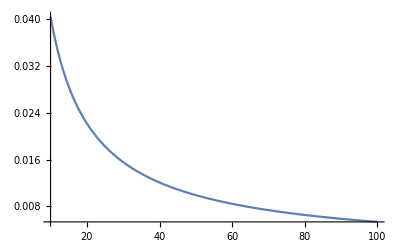

```mathematica
Plot[{ψ[x,0.2,0.1]},{x,10,100}]
```

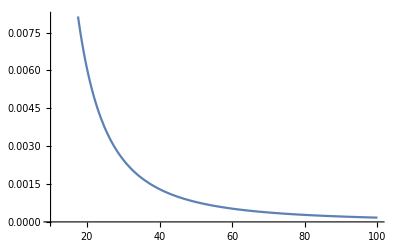

```mathematica
Plot[{ψ[x,1.2,0.5]},{x,10,100}]
```

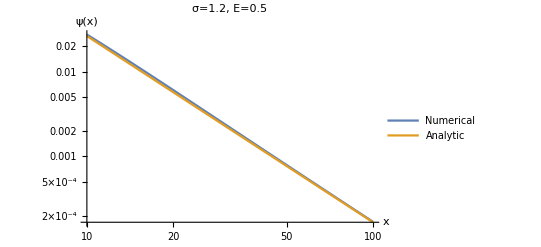

```mathematica
LogLogPlot[{ψ[x,1.2,0.5],-f[x,1.2,0.5]},{x,10,100},AxesLabel->{"x","ψ(x)"},PlotLegends->{"Numerical","Analytic"},PlotLabel->"σ=1.2, E=0.5"]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

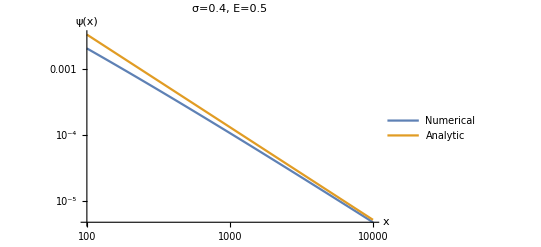

```mathematica
LogLogPlot[{ψ[x,0.4,0.5],-f[x,0.4,0.5]},{x,100,10000},AxesLabel->{"x","ψ(x)"},PlotLegends->{"Numerical","Analytic"},PlotLabel->"σ=0.4, E=0.5"]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

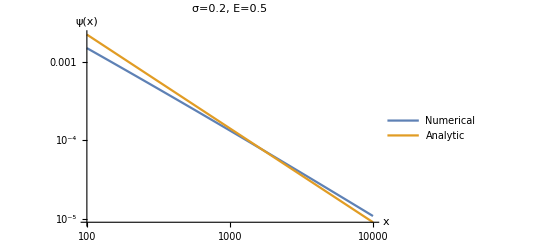

```mathematica
LogLogPlot[{ψ[x,0.2,0.5],-0.5*f[x,0.2,0.5]},{x,100,10000},AxesLabel->{"x","ψ(x)"},PlotLegends->{"Numerical","Analytic"},PlotLabel->"σ=0.2, E=0.5"]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

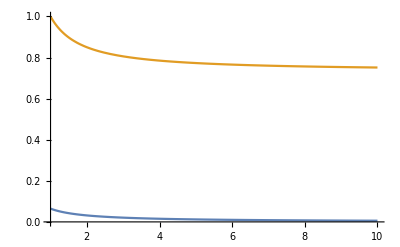

```mathematica
λ=1;
s=0.2;
ee=Abs[λ(1-(π(1+s))/λ^((1+s)/s))^(s/(1+s))];
eee=Λ(1/π-Λ^(σ-1));
Plot[{ψ[x,s,ee],ϕ[x,s,λ]},{x,1,10}]
```

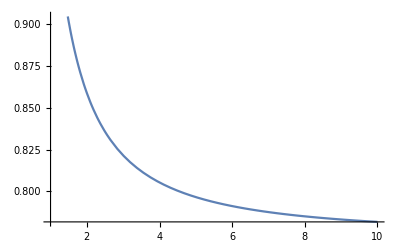

```mathematica
λ=1;
s=0.4;
ee=Abs[λ(1-(π(1+s))/λ^((1+s)/s))^(s/(1+s))];
Plot[{ϕ[x,s,λ]},{x,1,10}]
```

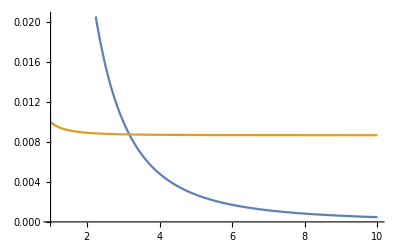

```mathematica
λ=1;
s=1.4;
ee=Abs[λ(1-(π(1+s))/λ^((1+s)/s))^(s/(1+s))];
Plot[{ψ[x,s,ee],0.01*ϕ[x,s,λ]},{x,1,10}]
```

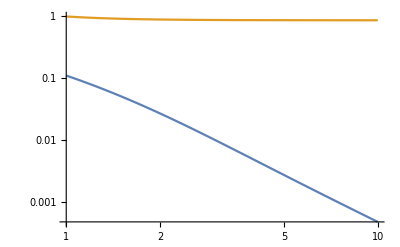

```mathematica
LogLogPlot[{ψ[x,s,ee],ϕ[x,s,λ]},{x,1,10}]
```

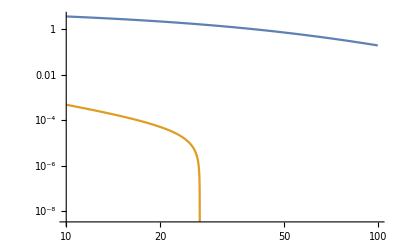

```mathematica
LogLogPlot[{ψ[x,1.4,0.01],ϕ[x,1.4,0.01]},{x,10,100}]
```

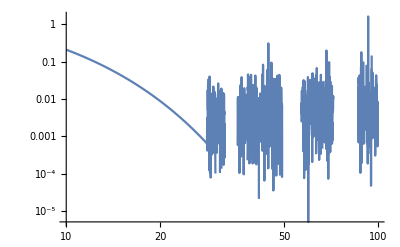

```mathematica
LogLogPlot[{ψ[x,2,0.1],ϕ[x,2,0.1]},{x,10,100}]
```

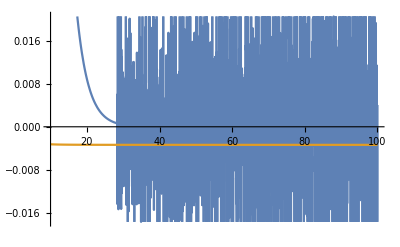

```mathematica
Plot[{ψ[x,2,0.1],ϕ[x,2,0.1]},{x,10,100}]
```

```mathematica
g[x_,σ_,ϵ_,a_]:=1/(x ϵ)Sin[a x]-a^σ/(x ϵ^2)Cos[a x]+(σ(σ-1)a^(σ-2))/(x^3 ϵ^2)Sin[a x];
```

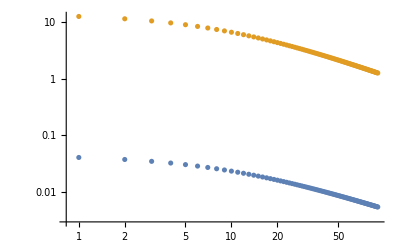

```mathematica
ListLogLogPlot[{Table[ψ[x,0.2,0.1],{x,10,100}],Table[Abs@g[x,0.2,0.1,π],{x,10,100}]}]
```

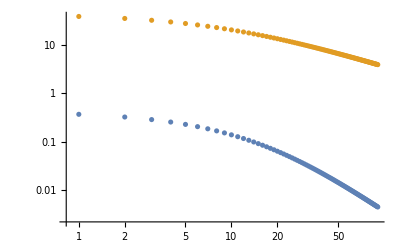

```mathematica
ListLogLogPlot[{Table[ψ[x,1.2,0.1],{x,10,100}],Table[Abs@g[x,1.2,0.1,π],{x,10,100}]}]
```

```mathematica
h[x_,σ_,ϵ_]:=1/(π(1-σ))1/(x^(1-σ)ϵ^((1-σ)/σ));
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

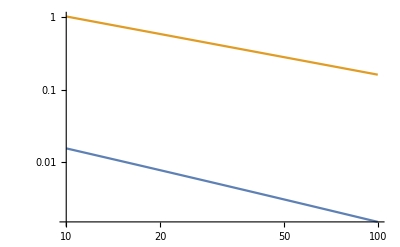

```mathematica
LogLogPlot[{ψ[x,0.2,0.5],h[x,0.2,0.5]},{x,10,100}]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

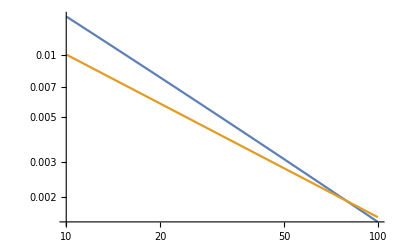

```mathematica
LogLogPlot[{ψ[x,0.2,0.5],0.01*h[x,0.2,0.5]},{x,10,100}]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

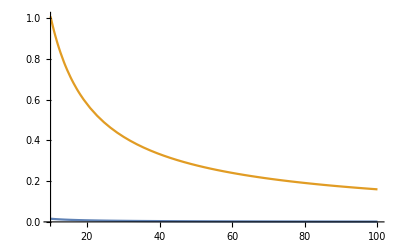

```mathematica
Plot[{ψ[x,0.2,0.5],h[x,0.2,0.5]},{x,10,100}]
```

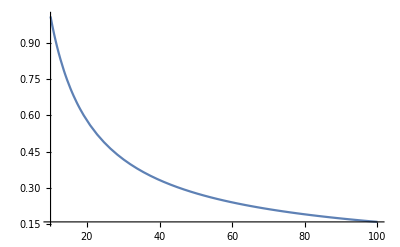

```mathematica
Plot[{h[x,0.2,0.5]},{x,10,100}]
```

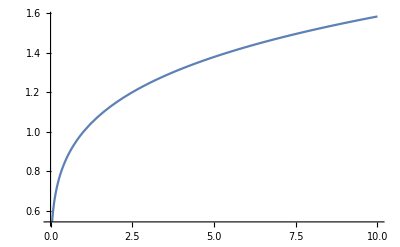

```mathematica
Plot[x^0.2,{x,0,10}]
```

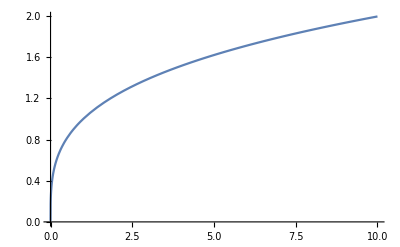

```mathematica
Plot[x^0.3,{x,0,10}]
```

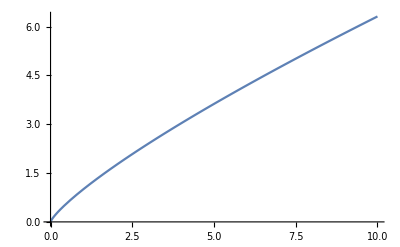

```mathematica
Plot[x/x^0.2,{x,0,10}]
```

```mathematica
Plot3D[{Λ(1/π-Λ^(σ-1)),0},{σ,0,3},{Λ,1,1000}]
```

-Graphics3D-

```mathematica
ⅈ^5
```

ⅈ